```mathematica
(* pdf modelling -- see eq. 79 of https://arxiv.org/pdf/0802.0161.pdf *)
f[x_,A_,alpha_,beta_,epsilon_,gamma_]:=A*x^(alpha-1)(1-x)^beta*(1+eps*Sqrt[x]+gamma*x)
```

```mathematica
testU=f[x,Aa,alphaa,betaa,epsilonn,gammaa]/.Aa->1/.alphaa->0.5/.betaa->3/.eps->0/.gammaa->0
int1U=Integrate[testU,{x,10^-4,1}]

testUbar=f[x,Aa,alphaa,betaa,epsilonn,gammaa]/.Aa->1/100/.alphaa->-0.35/.betaa->7/.eps->0/.gammaa->100
int1Ubar=Integrate[testUbar,{x,10^-4,1}]



testD=f[x,Aa,alphaa,betaa,epsilonn,gammaa]/.Aa->1/.alphaa->0.5/.betaa->3/.eps->0/.gammaa->0
int1D=Integrate[testD,{x,10^-4,1}]

testDbar=f[x,Aa,alphaa,betaa,epsilonn,gammaa]/.Aa->1/100/.alphaa->-0.35/.betaa->7/.eps->1/.gammaa->100
int1Dbar=Integrate[testDbar,{x,10^-4,1}]



testG=f[x,Aa,alphaa,betaa,epsilonn,gammaa]/.Aa->1/.alphaa->-0.25/.betaa->5/.eps->0/.gammaa->0
int1G=Integrate[testG,{x,10^-4,1}]
int2G=Integrate[testG*x,{x,10^-4,1}]

(* normalize to sum rules *)
xfU=x*f[x,Aa,alphaa,betaa,epsilonn,gammaa]/.Aa->(2+int1Ubar)/(int1U)/.alphaa->0.5/.betaa->3/.eps->0/.gammaa->0
xfUbar=x*testUbar

xfD=x*f[x,Aa,alphaa,betaa,epsilonn,gammaa]/.Aa->(1+int1Dbar)/(int1D)/.alphaa->0.5/.betaa->3/.eps->0/.gammaa->0
xfDbar=x*testDbar

int2U=Integrate[xfU,{x,10^-4,1}]
int2Ubar=Integrate[xfUbar,{x,10^-4,1}]
int2D=Integrate[xfD,{x,10^-4,1}]
int2Dbar=Integrate[xfDbar,{x,10^-4,1}]

xfG=x*f[x,Aa,alphaa,betaa,epsilonn,gammaa]/.Aa->(1-int2U-int2Ubar-int2D-int2Dbar)/int2G/.alphaa->-0.25/.betaa->5/.eps->0/.gammaa->0
```

(1-x)^3/x^0.5

0.894288

((1-x)^7 (100 x+1))/(100 x^1.35)

0.998142

(1-x)^3/x^0.5

0.894288

((1-x)^7 (100 x+√x+1))/(100 x^1.35)

1.0273

(1-x)^5/x^1.25

32.5407

0.323273

3.35255 (1-x)^3 x^0.5

((1-x)^7 (100 x+1))/(100 x^0.35)

2.26695 (1-x)^3 x^0.5

((1-x)^7 (100 x+√x+1))/(100 x^0.35)

0.340574

0.0309116

0.230291

0.0317563

(1.13361 (1-x)^5)/x^0.25

```mathematica
(* check sum rules *)
(xfU-xfUbar)/x
Integrate[%,{x,10^-4,1}]

(xfD-xfDbar)/x
Integrate[%,{x,10^-4,1}]

xfU+xfUbar+xfD+xfDbar+xfG
Integrate[%,{x,10^-4,1}]

(*Integrate[xfU,{x,10^-4,1}]
Integrate[xfUbar,{x,10^-4,1}]
Integrate[xfD,{x,10^-4,1}]
Integrate[xfDbar,{x,10^-4,1}]
Integrate[xfG,{x,10^-4,1}]*)
```

(3.35255 (1-x)^3 x^0.5-((1-x)^7 (100 x+1))/(100 x^0.35))/x

2.

(2.26695 (1-x)^3 x^0.5-((1-x)^7 (100 x+√x+1))/(100 x^0.35))/x

1.

((100 x+1) (1-x)^7)/(100 x^0.35)+((100 x+√x+1) (1-x)^7)/(100 x^0.35)+(1.13361 (1-x)^5)/x^0.25+5.61949 x^0.5 (1-x)^3

1.

```mathematica
xfU
xfUbar
xfD
xfDbar
xfG
```

3.35255 (1-x)^3 x^0.5

((1-x)^7 (100 x+1))/(100 x^0.35)

2.26695 (1-x)^3 x^0.5

((1-x)^7 (100 x+√x+1))/(100 x^0.35)

(1.13361 (1-x)^5)/x^0.25

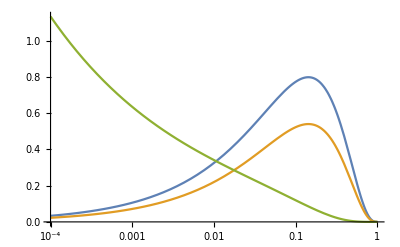

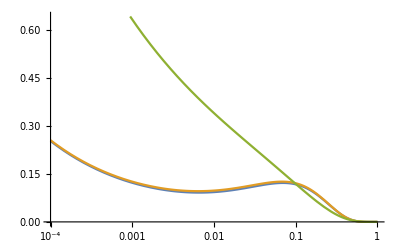

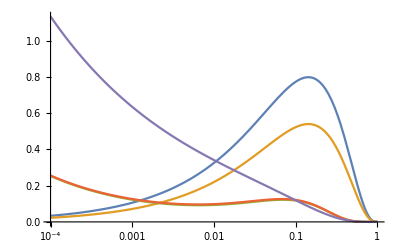

```mathematica
LogLinearPlot[{xfU,xfD,xfG/10},{x,10^-4,1}]
LogLinearPlot[{xfUbar,xfDbar,xfG/10},{x,10^-4,1}]
LogLinearPlot[{xfU,xfD,xfUbar,xfDbar,xfG/10},{x,10^-4,1}]
```